```mathematica
vars:={ζ3->1.202,η->6.1×10^-10,T0->2.3 10^-4,EI->13.6,Me->510999}
```

```mathematica
x=Solve[(1-Xe)/Xe^2==f,Xe] (*solve this quadratic formula*)
```

{{Xe→(-1-√(1+4 f))/(2 f)},{Xe→(-1+√(1+4 f))/(2 f)}}

```mathematica
sol=x[[2]]/.f->(2 ζ3)/π^2 η((2π T0(1+z))/Me)^(3/2)Exp[EI/(T0(1+z))]/.vars (*plug in f(z) and variables to the positive root of our solution*)
```

{Xe→(2.23756×10^22 ⅇ^(-59130.4/(1+z)) (-1+√(1+8.93832×10^-23 ⅇ^(59130.4/(1+z)) (1+z)^(3/2))))/(1+z)^(3/2)}

```mathematica
X=Xe/.sol
```

(2.23756×10^22 ⅇ^(-59130.4/(1+z)) (-1+√(1+8.93832×10^-23 ⅇ^(59130.4/(1+z)) (1+z)^(3/2))))/(1+z)^(3/2)

```mathematica
X[1500]
```

(2.23756×10^22 ⅇ^(-59130.4/(1+z)) (-1+√(1+8.93832×10^-23 ⅇ^(59130.4/(1+z)) (1+z)^(3/2))))/(1+z)^(3/2)[1500]

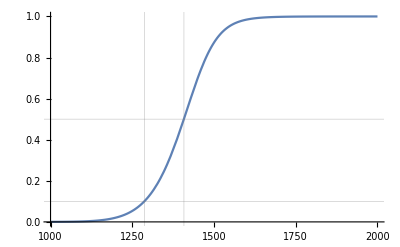

```mathematica
Plot[X,{z,1000,2000},
 GridLines->{{1287, 1408},{0.1, 0.5}}]
```

```mathematica
X/.z->1287 (*find redshift where ionization fraction is 0.1*)
```

0.100248

```mathematica
X/.z->1408 (*find redshift where ionization fraction is 0.1*)
```

0.50106

```mathematica
X/.z->267 (*value I got for part 5 of problem 1*)
```

3.92476×10^-39